```mathematica
data=Import["../fatal-police-shootings-data.csv"];
```

```mathematica
allDates=data[[2;;, 3]];
dates=Select[allDates,StringStartsQ[#,{"2016"}]&];
counts:=Counts[dates];
days:=366;
```

```mathematica
categories=KeySort[Append[Counts[Values[counts]], 0->days-Length[counts]]];
n=Max[Keys[categories]];
For[i=1,i<n,i++,If[KeyExistsQ[categories,i],None,categories[i]=0]];
{n,categories}
```

{8,<|0→26,1→76,2→75,3→86,4→60,5→27,6→10,7→4,8→2|>}

```mathematica
k=Sum[x*categories[x],{x,Keys[categories]}]/days;
{k,N[k]}
```

{321/122,2.63115}

```mathematica
a=Map[Function[x, (ⅇ^-k k^x)/(x!)],Range[0,n-1]];
a=Append[a,1-Accumulate[a][[-1]]];
expect=days*a;
n=Length[expect];
{N[a],N[expect]}
```

{{0.0719958,0.189432,0.249211,0.21857,0.143773,0.0756575,0.0331777,0.0124708,0.00571226},{26.3505,69.332,91.2113,79.9968,52.6208,27.6906,12.143,4.5643,2.09069}}

```mathematica
observe=Values[categories]
```

{26,76,75,86,60,27,10,4,2}

```mathematica
X2=∑_(i=1)^n (expect[[i]]-observe[[i]])^2/expect[[i]];
N[X2]
```

5.48168

```mathematica
P=1-CDF[ChiSquareDistribution[n],X2];
N[P]
```

0.790462

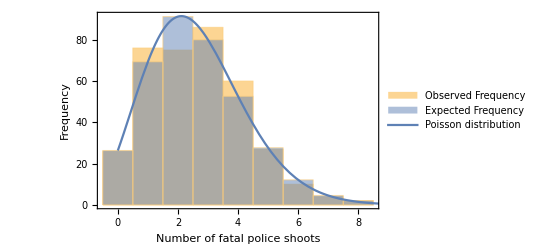

```mathematica
n=Length[observe];
weightedObserveData=WeightedData[Keys[categories],Values[categories]];
weightedExpectData=WeightedData[Range[0,n-1],expect];
fig=Show[
Histogram[
{Legended[weightedObserveData,"Observed Frequency"],
Legended[weightedExpectData,"Expected Frequency"]},n,
Frame->{True,True,False,False},
FrameTicks->{Range[0,n],Automatic},
FrameLabel->{"Number of fatal police shoots","Frequency"}
],
Plot[
Legended[Evaluate[days*PDF[PoissonDistribution[k],x]],"Poisson distribution"],{x,0,n+1},
PlotStyle->Thick,
PlotLegends->Automatic
]]
Export["q3-2016-exp.eps",fig];
```